```mathematica
(*
eps = e-2, e-6, e-17

[0; 1]

Begin
R1:=Exp((Degree(x,4)+2*Degree(x,3)-5*x+6)/5);
R2:=Coh(1/(-15*Degree(x,3)+10*x+5*Sqrt(10)));
VarF:=R1+R2-3;
End;
*)
```

```mathematica
(*Метод дихотомии*)
F[x_]:=Exp[(x^4+2 * x^3 - 5*x+6)]+
Cosh[1/(-15*x^3+10*x+5*Sqrt[10])]-3;
Dexot[precision_]:=Module[{graphValues, NonGraphValues},
eps = 10^-precision;
delta = eps/5;
leftBound = 0;
rightBound = 1;
nextLeftBound[a_, b_]:=(a+b)/2-delta;
nextRightBound[a_, b_]:=(a+b)/2+delta;
IterationCountrer = 0;
intervals= List[];
AppendTo[intervals, {leftBound,rightBound}];

graphValues=List[];
NonGraphValues=List[];
While[(rightBound -leftBound) > eps,
nextLeft = nextLeftBound[leftBound, rightBound];
nextRight = nextRightBound[leftBound, rightBound];
leftFunc = F[nextLeft];
rightFunc = F[nextRight];
If[leftFunc <= rightFunc,
rightBound=nextRight;
AppendTo[graphValues, {rightBound, rightFunc}];
AppendTo[NonGraphValues, {nextLeft, leftFunc}];
,
leftBound = nextLeft;
AppendTo[graphValues, {nextLeft, leftFunc}];
AppendTo[NonGraphValues, {rightBound, rightFunc}];
] ;
AppendTo[intervals, {leftBound,rightBound}];
++IterationCountrer;
];
If[Length[intervals]>80,
temp = List[];
For[i = 1, i < Length[intervals], i+=2,
AppendTo[temp, intervals[[i]]];
];
intervals = temp;
];
Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
Print["Answer: ",NumberForm[Subscript[y, min],{25, precision}],"\nIterations: ", IterationCountrer, "\nFunction calculations: ", IterationCountrer * 2, "\nPrecition: ", precision, "\nx_min = ",Subscript[x, min] ];
(*Return[SetPrecision[N[F[rightBound-leftBound]],20]];*)
Print[Show[
DiscretePlot[intervals[[k]], {k, 1,Length[intervals]}, AxesLabel->{iteration, interval}, GridLines->Automatic], Graphics[Table[Line[{{k, intervals[[k]][[1]]},{k, intervals[[k]][[2]]}}], {k, 1, Length[intervals]}]]]];
Return[
Show[Plot[F[x], {x, 0.4, 1.1}, PlotRange->{{0.4, 1.1},{0,80}}],
ListPlot[{{Subscript[x, min], Subscript[y, min]}}, PlotStyle->{Black},PlotLegends->{"minimum"} ],
AxesLabel->{"x","y"}
]
];
];
(*
ListPlot[{ graphValues,NonGraphValues},PlotStyle->{Red, Green},PlotLegends->{"included in calculations","excluded from calculations"}],
*)
```

Null

```mathematica
(*Метод дихотомииб результаты*)
```

Answer: 28.27
Iterations: 8
Function calculations: 16
Precition: 2
x_min = 0.7470546875

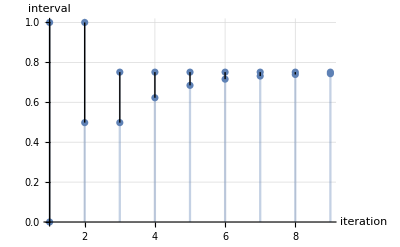

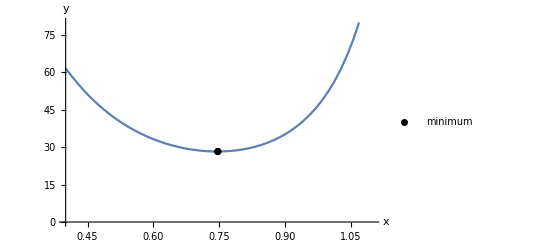

```mathematica
(*Погрешность 0.01*)
Dexot[2]
```

Answer: 28.267932
Iterations: 21
Function calculations: 42
Precition: 6
x_min = 0.74601044351167678833

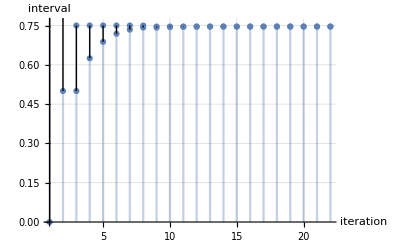

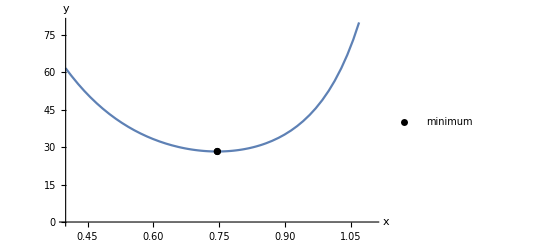

```mathematica
(*Погрешность 10^-6*)
Dexot[6]
```

Answer: 28.26793230872697482
Iterations: 58
Function calculations: 116
Precition: 17
x_min = 0.74601022407293920014

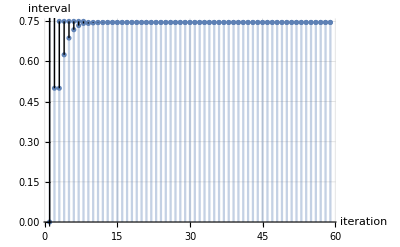

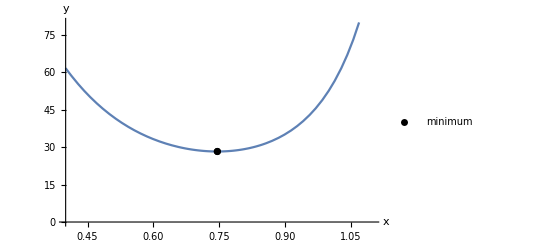

```mathematica
(*Погрешность 10^-17*)
Dexot[17]
```

```mathematica
(*Метод золотого сечения*)
GoldenRat[precision_]:=Module[{},
eps = 10^-precision;
leftBound = 0;
rightBound = 1;
intervals=List[];
goldenRat = (1+Sqrt[5])/2;
nextLeftBound[a_, b_]:=a + (1 - 1/goldenRat)(b-a);
(*a+(b-a)/(goldenRat+1);*)
nextRightBound[a_, b_]:= a +(b-a)/goldenRat;
(*b-(b-a)/(goldenRat+1)*);
leftFunc = F[leftBound];
rightFunc = F[rightBound];

nextLeft = nextLeftBound[leftBound, rightBound];
nextRight=nextRightBound[leftBound, rightBound];
(*leftBound+rightBound-nextLeft;*)

If[nextRight<nextLeft,
temp= nextLeft;
nextLeft = nextRight;
nextRight = temp;];

nextLeftFunc = F[nextLeft];
nextRightFunc = F[nextRight];
next = 0;nextF = 0;

AppendTo[intervals, {leftBound,rightBound}];
If[nextLeftFunc <= nextRightFunc,
rightBound=nextRight;
next = nextLeft;
nextF = nextLeftFunc;
graphValues={{rightBound, nextRightFunc}};
NonGraphValues={{next, nextF}};
,
leftBound = nextLeft;
next = nextRight;
nextF = nextRightFunc;
graphValues={{rightBound, nextRightFunc}};
NonGraphValues={{next, nextF}};
] ;
IterationCountrer = 1;

While[(rightBound -leftBound) > eps,
nextNew=leftBound+rightBound-next;
nextNewF = F[nextNew];
If[nextNew <= next, 
nextLeft = nextNew;
leftFunc= nextNewF;
nextRight = next;
rightFunc = nextF;
,
nextLeft = next;
leftFunc= nextF;
nextRight = nextNew;
rightFunc = nextNewF;
];

If[leftFunc <= rightFunc,
rightBound=nextRight;
next = nextLeft;
nextF = nextLeftFunc;
AppendTo[graphValues,{nextRight, rightFunc}];
AppendTo[NonGraphValues,{next, nextF}];
,
leftBound = nextLeft;
next = nextRight;
nextF = nextRightFunc;
AppendTo[graphValues,{nextLeft, leftFunc}];
AppendTo[NonGraphValues,{next, nextF}];
] ;
AppendTo[intervals, {leftBound,rightBound}];
++IterationCountrer;
];

Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
Print["Answer: ",NumberForm[Subscript[y, min],{25, precision}],"\nIterations: ", IterationCountrer, "\nFunction calculations: ", IterationCountrer +1, "\nPrecition: ", precision, "\nx_min = ",Subscript[x, min] ];
If[Length[intervals]>50,
temp = List[];
For[i = 1, i < Length[intervals], i+=2,
AppendTo[temp, intervals[[i]]];
];
intervals = temp;
];
Print[Show[
DiscretePlot[intervals[[k]], {k, 1, Length[intervals]}, AxesLabel->{iteration, interval}, GridLines->Automatic], Graphics[Table[Line[{{k, intervals[[k]][[1]]},{k, intervals[[k]][[2]]}}], {k, 1, Length[intervals]}]]]];

Print[Show[Plot[F[x], {x, 0.4, 1.1}, PlotRange->{{0.4, 1.1},{0,80}}],
ListPlot[{{Subscript[x, min], Subscript[y, min]}}, PlotStyle->{Black},PlotLegends->{"minimum"} ],
AxesLabel->{"x","y"}
]];
Return[Subscript[y, min]];
];
```

Answer: 28.38
Iterations: 10
Function calculations: 11
Precition: 2
x_min = 0.767997331878101978

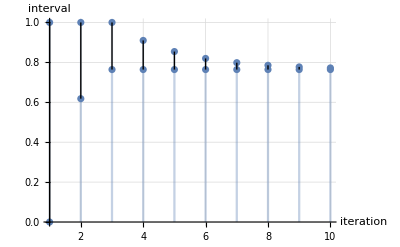

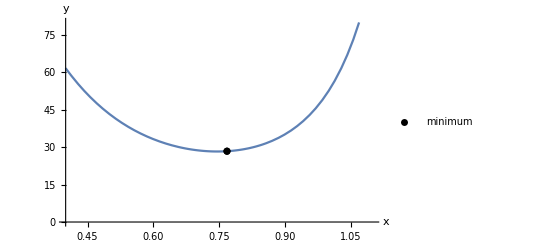

```mathematica
(*Метод золотого сечения, результаты*)
(*Погрешность 0.01*)
GoldenRat[2];
```

Answer: 28.344882
Iterations: 29
Function calculations: 30
Precition: 6
x_min = 0.76393245733916

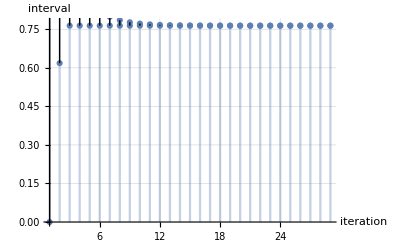

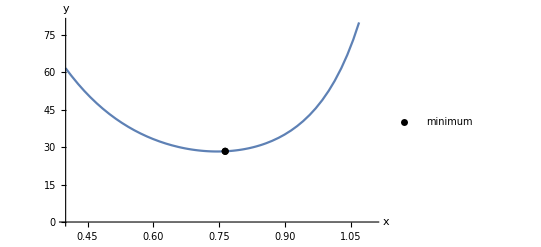

```mathematica
(*Погрешность 10^-6*)
GoldenRat[6];
```

Answer: 28.34487871954423147
Iterations: 82
Function calculations: 83
Precition: 17
x_min = 0.764

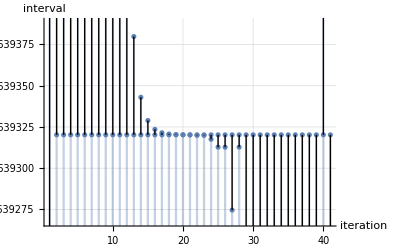

-Graphics-

```mathematica
(*Погрешность 10^-17*)
GoldenRat[17];
```

```mathematica
(*
Вывод

Ни один из методов не дает точный ответ, так как результат получается сравнением значений функции в конечном числе точек.

Из результатов работы программ следует, что метод золотого сечения эффективнее, чем метод дихотомии. Совершается меньше вычислений функций и итераций. Теоретический материал учебника "Введение в методы оптимизации" (А.В.Аттеков и др.) подтверждает это.
*)
```

```mathematica
FindMinimum[F[x], {x, 0, 1}]
```

{28.2679,{x→0.74601}}